## Playing with precomputed g values

### Downloads and Installations

```mathematica
(*ResourceFunction["MaTeXInstall"][]*) (* Run if need to install MaTeX*)
<<MaTeX` (* Run to call MaTeX*)
```

Recursion/JuliaRecursion/recursion.jl, we compute g values and append them to the file “computedG.csv”. In this file, we import the data from this file just to look at it. Recall that for the computation, we store polynomials as arrays; that is, a+bk+ck^3 == {a,b,0,c}. For viewing purposes, in this file, we convert them back to polynomials in k.

```mathematica
Remove["Global`*"];
```

```mathematica
gFilename="/Users/jtiosue/Documents/Repositories/LXEB/Recursion/JuliaRecursion/computedG.csv";
g=Association@@Table[
{tup[[1]],tup[[{2,3,4}]]}->∑_(i=0)^(Length[tup]-5) tup[[5+i]] k^i,
{tup,Import@gFilename}
];
```

```mathematica
(*gFilename="/Users/jtiosue/Documents/Repositories/LXEB/Recursion/MathematicaRecursion/computedG.csv";
g=Association@@Table[
tup[[1]]->∑_(i=0)^(Length[tup[[2]]]-1) tup[[2]][[i+1]] k^i,
{tup,ToExpression@Import@gFilename}
];*)
```

### How many have we computed so far?

```mathematica
g//Length
```

16575

### Print all of the a={0,0,0} entries

```mathematica
ns=Select[Keys@g,#[[2]]=={0,0,0}&][[All,1]]//Sort;
```

```mathematica
Table[
{n,g[{n,{0,0,0}}]},
{n,ns}
]//TableForm
```

1 | 2 k+2 k^2
2 | 176 k+184 k^2+64 k^3+8 k^4
3 | 74880 k+90336 k^2+40752 k^3+8976 k^4+1008 k^5+48 k^6
4 | 90408960 k+121065984 k^2+63951360 k^3+17759616 k^4+2872320 k^5+278016 k^6+15360 k^7+384 k^8
5 | 237617971200 k+343673303040 k^2+202717824000 k^3+65407180800 k^4+12943123200 k^5+1655781120 k^6+139392000 k^7+7603200 k^8+249600 k^9+3840 k^10
6 | 1159859699712000 k+1780791422976000 k^2+1140813555425280 k^3+410191172628480 k^4+93270554265600 k^5+14247651916800 k^6+1508640215040 k^7+112075453440 k^8+5807462400 k^9+203443200 k^10+4423680 k^11+46080 k^12
7 | 9462639862480896000 k+15246273259929600000 k^2+10421808429874544640 k^3+4071608172016680960 k^4+1026952754189967360 k^5+178307659157483520 k^6+22109565749483520 k^7+1998175940167680 k^8+132745496647680 k^9+6466813839360 k^10+227377059840 k^11+5549967360 k^12+85800960 k^13+645120 k^14
8 | 119720630833266032640000 k+200796561000272756736000 k^2+144711123926956218777600 k^3+60415241009583386787840 k^4+16528349328270038138880 k^5+3166169317852953968640 k^6+441843922442755768320 k^7+46026366788113367040 k^8+3629790873271664640 k^9+218065033148497920 k^10+9969100754780160 k^11+343607014195200 k^12+8742088212480 k^13+157223485440 k^14+1816657920 k^15+10321920 k^16
9 | 2221247018056830041456640000 k+3855175197947055480766464000 k^2+2904237338727171996883353600 k^3+1280729580277534827070095360 k^4+374303224008993996354355200 k^5+77564194739580892836003840 k^6+11877470107076545413120000 k^7+1380287720700295139819520 k^8+123832881173454682521600 k^9+8665188337608815738880 k^10+475146042332361523200 k^11+20406933381977210880 k^12+682378385994547200 k^13+17534066558238720 k^14+337908282163200 k^15+4664186634240 k^16+41803776000 k^17+185794560 k^18
10 | 57875363345940374711225548800000 k+103476098681327348341580759040000 k^2+80965230375737197759140200448000 k^3+37396163878121465462090052403200 k^4+11549033918313096837275320320000 k^5+2553455926152348117269741568000 k^6+421694240195528846498856960000 k^7+53496251894559728028037939200 k^8+5312875561161631329484800000 k^9+418297517171370849632256000 k^10+26311610109360809705472000 k^11+1327075152807942468403200 k^12+53660329481243197440000 k^13+1732280071673217024000 k^14+44252111014723584000 k^15+880831333741363200 k^16+13306420592640000 k^17+145421402112000 k^18+1040449536000 k^19+3715891200 k^20
11 | 2045846254375871026944282722304000000 k+3754756022542427749718469220761600000 k^2+3036540816683854203446772734361600000 k^3+1459584741451196867679383099277312000 k^4+472477053335440502937507615630950400 k^5+110338850085947626637087851570790400 k^6+19408962083693217370343998488576000 k^7+2647105238020097389884208054272000 k^8+285604538987756004915330573926400 k^9+24722331120708172694587205222400 k^10+1733426526911822577735892992000 k^11+99042015520504682810376192000 k^12+4624794687268006821848678400 k^13+176490204956714899301990400 k^14+5487825810170990297088000 k^15+138150937332359626752000 k^16+2785665572983170662400 k^17+44232479114290790400 k^18+537960233631744000 k^19+4770498281472000 k^20+27876615782400 k^21+81749606400 k^22
12 | 95391755978551627984315810937044992000000 k+179204566298221128108188538543852748800000 k^2+149211417132572995348096252025556172800000 k^3+74269070732332919813012637280565723136000 k^4+25043132500802798445487604296060187443200 k^5+6130332032327408168402186331644284108800 k^6+1137970861000694185537909022671031500800 k^7+164994391466771392603106045989591449600 k^8+19079536338562466167577024543273779200 k^9+1786298200347404901271609828756684800 k^10+136870721872567023351054350470348800 k^11+8647530520047195308963658832281600 k^12+452660108928649181781340402483200 k^13+19677990448219037704559316172800 k^14+710489959309228528850750668800 k^15+21258602346398524390873497600 k^16+524601391220488492233523200 k^17+10593145227495451970764800 k^18+172953716869355588812800 k^19+2242267733870877081600 k^20+22429460312830771200 k^21+164626703371468800 k^22+800492145868800 k^23+1961990553600 k^24
13 | 5731225923923558774941392274715364556800000000 k+10995285392857893153955248685346237448192000000 k^2+9396291655808965095857136949412775120076800000 k^3+4823815933413165634688518642221969309696000000 k^4+1686045017910136620172834418161358173372416000 k^5+430058190086748619438675818711864313066291200 k^6+83645952925319049329502297583443614525030400 k^7+12783496470888327284800570983293708874547200 k^8+1568365356359712581337663330310042524057600 k^9+156911530060590982522321872019058904268800 k^10+12951188717221020170081063931182736998400 k^11+889402203491379787392669332937061171200 k^12+51123876481473485233393645287741849600 k^13+2469279906078287574326646394375372800 k^14+100414246857345028777569369351782400 k^15+3438485145193302858001225560883200 k^16+98981123012613172252367231385600 k^17+2386435230358072393509686476800 k^18+47901928622817660568495718400 k^19+793419435675853983527731200 k^20+10705955428609057986969600 k^21+115483486268174421196800 k^22+966895361054893670400 k^23+5971027875279667200 k^24+24536653863321600 k^25+51011754393600 k^26
14 | 435016381900506856831866584394857505557053440000000 k+850641028100102107599405928590873158561562624000000 k^2+744177677930000410594651099246438476934230835200000 k^3+392765934940263200309086966908864137645072056320000 k^4+141740164249577464900211506111838387825591451648000 k^5+37493148697132609766465931507814730382168607948800 k^6+7597851558902861415701751133564594587074297856000 k^7+1215825186432182467595066663143504988364550963200 k^8+157024523449803421413981166889468636090597376000 k^9+16634253576618990270219734078166208622886912000 k^10+1463069617573437699170674414460307121373184000 k^11+107829884801953134624830915120306552045568000 k^12+6704872949713068320442207470552881299456000 k^13+353460585217411756368615210273120190464000 k^14+15848270560956045928785182794306289664000 k^15+605395215484940758719723060011728896000 k^16+19706010712997242975338011239120896000 k^17+545882883444642686423346916098048000 k^18+12831768021906489769491739705344000 k^19+254754412321883136950714499072000 k^20+4242568218864654435112452096000 k^21+58698815345837682060165120000 k^22+665683785032527043887104000 k^23+6068550264995614556160000 k^24+43153979244206358528000 k^25+227331434890867507200 k^26+799864308891648000 k^27+1428329123020800 k^28
15 | 41015423552674622914217007993321376654552989696000000000 k+81613496237916814279430189403710232698076769812480000000 k^2+72935761736795099434027426505273001970382596472832000000 k^3+39469167746786016789673464713765044161807115301683200000 k^4+14658489647149365369688134226458018866014452417822720000 k^5+4005642374982347571306303006413308386663757705641984000 k^6+841894008369147689651597769986278088816180015923200000 k^7+140314899731321919218954100732589805676646147031040000 k^8+18958724346586671613395879609136034078693177425920000 k^9+2111287213433663243286190556005935537597978771456000 k^10+196239008525105625054941044900553187120906240000000 k^11+15371809678935519387240534148764753205395456000000 k^12+1022320603718009549911127670751367330896281600000 k^13+58049535178022196007860213139681051630632960000 k^14+2825641405486138851904157325371731083264000000 k^15+118224870574226811803586692429170448793600000 k^16+4257915065406086597360800798054809600000000 k^17+132032020524898697644647263211796561920000 k^18+3521455664436908154050817819672576000000 k^19+80598885646750705233704706165964800000 k^20+1577163950259190692632000357990400000 k^21+26242986144319150133970374492160000 k^22+368545153781264680341209088000000 k^23+4324073226748208292770611200000 k^24+41797618501349598434426880000 k^25+326291846083558187728896000 k^26+1995254019802320076800000 k^27+9071961008410460160000 k^28+27638168530452480000 k^29+42849873690624000 k^30
16 | 4733947668708623751912773749104507960673951480283136000000000 k+9572121146818022231413096633182940477582481401105612800000000 k^2+8722611884676960450209963376856805950266355162514718720000000 k^3+4828903632596756368656355815413759364904358402127298560000000 k^4+1840681287318135512724578262401896933122645982397752934400000 k^5+517963117075959515715135702250245284267744468767415992320000 k^6+112488913259021610002120123546629803137978360916709736448000 k^7+19442026206219797225096010211957782127801624126436671488000 k^8+2734536361931891443707233237393241948886853161247047680000 k^9+318289474177404575559710212344099684391952615252951040000 k^10+31056908074957593606793990585042650517048470181773312000 k^11+2565971981803943748666978423521021197264984674926592000 k^12+180930174168994818783921846866585292638408146944000000 k^13+10954249547070396622726825731428275561215452774400000 k^14+572115713653829528266115522295147569496163614720000 k^15+25863660458514664361102436869823200527877406720000 k^16+1014359836255883015912254280636584548315955200000 k^17+34556588550060295913096287790410245970329600000 k^18+1022847702654201040964375127133852312535040000 k^19+26284280966177681095700557477600234045440000 k^20+585309581173955399237513562478451097600000 k^21+11260804451313618112071067594496409600000 k^22+186360997567616093805575135790366720000 k^23+2637280377366585367876768754565120000 k^24+31660734895175380753436796518400000 k^25+319044332488810634736335585280000 k^26+2660184807290552898721677312000 k^27+17983949526179630045724672000 k^28+95576526715280393502720000 k^29+378888867142183157760000 k^30+1009200225161576448000 k^31+1371195958099968000 k^32
17 | 660369928361921038663125824388827945277225616394491527168000000000 k+1355254392444899932822314181690016794053219678272721675878400000000 k^2+1257316070374719779964553217456957197943020529194120469544960000000 k^3+710725654956843052674692999783164736429788700873204957184000000000 k^4+277421714198930563347805305769910682079570358332132028527411200000 k^5+80174271820417175846680405601605642693324826120502635774607360000 k^6+17935817855113565771427182846175028445393086506285638199803904000 k^7+3203185565966353273094373357027085392477172740483205746917376000 k^8+467063899147655534745415710809795765517895680382744601296896000 k^9+56555488989877278557265540038154405572346624178945190264832000 k^10+5762088815318406334542731564948948981729993246319581331456000 k^11+499081830099303565922201743126038392974092345518025867264000 k^12+37050801281119501969907840581139984282746438914643329024000 k^13+2372835930813549818385795925100405671913398407505379328000 k^14+131761820997718813274338251828734219534830324898856960000 k^15+6368856968114119998431734761889380658027485085040640000 k^16+268742790706872598032812331824326969058430434672640000 k^17+9918974093935687692386602768288011849098676142080000 k^18+320572036845053534876506518857652356838347243520000 k^19+9074474373857277545477999037746034964200161280000 k^20+224849858747704188231950358621077856615137280000 k^21+4869565024077920836336903771901854388060160000 k^22+91948476841650748151719597635726276034560000 k^23+1508385983520034968385171686142550999040000 k^24+21394309252421729382872424472054333440000 k^25+260697662474196898016950739502366720000 k^26+2706565603710494053420858160971776000 k^27+23681112468840411830912437714944000 k^28+172076483870870955082408525824000 k^29+1017257896210775636189380608000 k^30+4742195614582683230797824000 k^31+16535789567543089299456000 k^32+38835011925307293696000 k^33+46620662575398912000 k^34
18 | 110090682939561549172291809392308736856602055796081839864545280000000000 k+229075779417446271108957793124869480874606917747250670109458432000000000 k^2+216075320700789631152349088496121435233300031851074226002853888000000000 k^3+124510584088462545445958630234996391671812693695016964306459688960000000 k^4+49671525342447303446305970730155099389130005112505254233434488832000000 k^5+14709201131564900607453633505619062041027008858544712028433206476800000 k^6+3380731441198709806559469641103744632500364401079096433189480038400000 k^7+622006236990384356797605125549365590953199541653395191078808715264000 k^8+93702773441914145589846300544921664127026774884268385812367802368000 k^9+11757637217664039511158414792068553862244052592876819964906962944000 k^10+1245312005228014948587541839813073473837786894607163659357519872000 k^11+112511905917118195710725562333464380208736174390749196774801408000 k^12+8744503565814431613536154325831645561104667909495670358147072000 k^13+588602507964122311471914532861366565696759566088836560715776000 k^14+34499273639479199079876687139122861963376692793866650124288000 k^15+1768327706623647441496423124265118682901418096749988282368000 k^16+79529192691820622447674173867134428195489037874332958720000 k^17+3146135807850476757588156147301675771896914459240693760000 k^18+109661359947004262654892440210092069314013632009338880000 k^19+3371123875712759493019441192395666705864777007104000000 k^20+91421828012880717321755959027353852917889147863040000 k^21+2186127164517580511958519266864933768626773688320000 k^22+46038508644496892522089881580559992956817244160000 k^23+852129994935107554091382425384674106718289920000 k^24+13821548079350798602301472259710141144760320000 k^25+195682694394423052744473471802467428597760000 k^26+2405692732577571033575353814205994106880000 k^27+25510304825474886191803487053619920896000 k^28+231336116528167197705528216536481792000 k^29+1774064993730795034957199846670336000 k^30+11334996813443418001247481888768000 k^31+59094748902567169978439565312000 k^32+243607807094319224023154688000 k^33+752983934488739844194304000 k^34+1570929846140641738752000 k^35+1678343852714360832000 k^36
19 | 21715671842695404548476821436081991661655715162190967680524510822400000000000 k+45771873979219004951872736946005142731922989939452851845403405975552000000000 k^2+43844872524686973443303083085618315907984544035711777456037555706265600000000 k^3+25718537119320731477872897266496296790588706485949760441938339105341440000000 k^4+10468415404524027812740889947048340327450072254502836137132865408204800000000 k^5+3170314619981162635969743670846716121975520309095445483056032127962316800000 k^6+746940950563758011602118963681264997763878362681450370649818793236234240000 k^7+141216148537712131288629731136749831705730055866979510871978146850144256000 k^8+21915338927903127097735069328866167686936992417500493893340843412029440000 k^9+2840303670135974850837772448981329489697818188738765633257843095240704000 k^10+311584398569108979588785848523993241879090521459352739389553728552960000 k^11+29243157145609971728227768835005939078730423786541683744094591909888000 k^12+2368359561066083476705010677996480359554262484377845353283038740480000 k^13+166676884722390264705250813821180304142094289827624411502888353792000 k^14+10251040865662810460973344090363172958091031138527161933941964800000 k^15+553497514753955188183148494953613922823342722618455950775812096000 k^16+26333571794599945644077183814453547523747624494233657047777280000 k^17+1107117828221508030494105758013812208824501943160811882020864000 k^18+41219264564313075232246191420324186433092399011445551923200000 k^19+1361051940227939684123300282123564974138664627862755082240000 k^20+39892504573524630346337070437331225539813807002484736000000 k^21+1038146819184108588828376915641975870832948570918748160000 k^22+23978314049028715157861724453858049906793179093401600000 k^23+491060539973446165772285647981025544734393090703360000 k^24+8901749605692230609777833095336864015768040243200000 k^25+142488662768161666446898152054763586185529917440000 k^26+2007337412784420301507990826056075279136194560000 k^27+24781928653476574151081572373339084710477824000 k^28+266653709848793473907454682381716459356160000 k^29+2483377038725729610876457366303084118016000 k^30+19841952706605185156508672436564131840000 k^31+134470427542182888532655761325555712000 k^32+761395291702891260118989243678720000 k^33+3526937190654496082240741572608000 k^34+12949003782415910894881996800000 k^35+35724022197991635758874624000 k^36+66647034391287268638720000 k^37+63777066403145711616000 k^38
20 | 5023150887754774704270983325708029401095405914989142597521624742756352000000000000 k+10716336940747447794241093248396606553054873474529161164787900309737308160000000000 k^2+10413914904357387572547362924538724804871620201889317661506642300234629120000000000 k^3+6210523689426713762307668741010571861431993434027741900289699504845330841600000000 k^4+2575501357547166221819972805187992552745290735873741070491213805925066342400000000 k^5+796322930798790812222982965990449572985389591210860909299854962413686226944000000 k^6+191953664815702501407269833142985523282283922145009540387320869747272187904000000 k^7+37209738035342315011053269789465151392524173875191829830551825063272188477440000 k^8+5934068194350227071590399104191593288607545139315130745164854534990725120000000 k^9+792156495846758905423717942183147577981257730569326602633557143064884019200000 k^10+89726703220668030733898100753040837317181906617633587494428173839997337600000 k^11+8717352013225969354084678605790031320648171564598842729507915050547937280000 k^12+732828444302431658194312353506290877123929707537353274769046274834432000000 k^13+53688296782838471680189760641310347433257987056077410362833545828761600000 k^14+3447965399692238763211911890503902769816044386802274964559188774092800000 k^15+195047500460747655732634151231450983444817389462347975037708633374720000 k^16+9756974713000430407356816054506750533405431863037309189743443968000000 k^17+432970893123873694424490004015447254440691435249105539918148403200000 k^18+17086372418485669223011601284520229626987174611101412784445849600000 k^19+600762954603477141782678251301007224909522873313604634054492160000 k^20+18844635603006686181835470499297385545763484481339502100480000000 k^21+527763480621089098262342000329687305739263875112719351808000000 k^22+13199730244644669654422288324243382470305312487730315264000000 k^23+294742077491511820537498707485188598203446416305343692800000 k^24+5870972373919406688041283931862024709464668671836160000000 k^25+104173062653863053037152684990440816837789082451968000000 k^26+1643194925277673267581881929516246366992205873152000000 k^27+22978023779668624209778550686897417682377097871360000 k^28+283839547840461734972761332677890126129397760000000 k^29+3083177507657569370304626239941571402058956800000 k^30+29282839566466167982175147372083927213670400000 k^31+241441400250471913817370513794087277035520000 k^32+1712681469773614625022919457120452608000000 k^33+10332037051255414735550109081560678400000 k^34+52204491770159543462282141053747200000 k^35+216288072705435587792148187054080000 k^36+711751550842574916468867072000000 k^37+1763359353567295151328460800000 k^38+2959255881105961018982400000 k^39+2551082656125828464640000 k^40
21 | 1351672242568267466106996368460675711567398344708341051500710574192622305280000000000000 k+2916573457621717520007723218398897272261475052655041442346863155782470755942400000000000 k^2+2872717796229232654835872083615199327806946034250846722973718213412338406522880000000000 k^3+1739877437405426424206803799785654902030431252677535877885892254117329891229696000000000 k^4+734166494779832243870036881643889075469253245155574657921649764518750573507379200000000 k^5+231412664785364219277443053575940336287243297040970668379859745994522881488322560000000 k^6+56975450431074968486018888431610546035261671089234800690945530860059758723858432000000 k^7+11302785801349586432191426500644157760442863028662136447885679427101761045161574400000 k^8+1848362177388347551006898861249828845639707957100306856746721386937437558753198080000 k^9+253542479577437611770297623525288829046156316644803422935627704478693652409876480000 k^10+29573625565807281401246658312489833431642374641287288344197572010891163362918400000 k^11+2965471183499070120026059681278144833466354722726635683666920447187750381158400000 k^12+257912991118269070049687349370936641788741857727176464300484910764915855196160000 k^13+19597819199060378374610849290982287935095061539687242043646317271019432181760000 k^14+1308916313441037247880043165943375640471884939200681224237836235372180275200000 k^15+77223813887442017452189979137537330924848700139999447249822691958456320000000 k^16+4041258596595841830388621667092317046348227251663360192043738775305584640000 k^17+188225737437003902918187387329292900488348436003751323751543241692938240000 k^18+7824027451200615396039397009409214006927126165055817433234413086310400000 k^19+290880170377770817778984252814541023898267057951939882018476864307200000 k^20+9688286883064803443963329786735709499684168725992664923736710840320000 k^21+289423765855485898209084002190283245598081103932882520340399390720000 k^22+7760303181547553718676211289683652110295929362321058285223936000000 k^23+186803611116350991749189580692229278054631978991908040998912000000 k^24+4036077544309877475207944409501903356288932640262064806297600000 k^25+78217081125989117822691184085562766584268738462196799897600000 k^26+1357984168046735448831001826739439618710471156078477312000000 k^27+21085639176074034102458459171909744840797377632246169600000 k^28+292122421517240507469265221154524749578330567102955520000 k^29+3600145633158137536354785632902224078914190437253120000 k^30+39318738782596835763128441932915209568742119833600000 k^31+378741193487951243090621398234835384603875737600000 k^32+3198832707629662622009617429455476476021309440000 k^33+23516229126880790572205636986233451016355840000 k^34+149102814367010865847097857412594191564800000 k^35+805862908627002341966649016040030208000000 k^36+3655955915037796145473318735010856960000 k^37+13628042285739284423309912294031360000 k^38+40425881416001427208664619417600000 k^39+90437206722641804502289612800000 k^40+137253349064881823054561280000 k^41+107145471557284795514880000 k^42
22 | 420054443444910096866871720424931521746526665364502859964460227581761310204887040000000000000 k+916131977483748446097296610102808103913697597422275266885135419200193693161304883200000000000 k^2+913857735845195300771829759016857234592712557346718344208155649202757358235932426240000000000 k^3+561557705203507472268050630856211778293863232507576728810153926174098085334931734528000000000 k^4+240835836172023794305894897908559545507231843617797318663374288282628973449983924633600000000 k^5+77288498365391829754519196087100151769616117419081684150410436866754781906383803514880000000 k^6+19407481103333118729092700041254474240421574960384077770024608304790706449373972135936000000 k^7+3933546083432976570299623020555873185314076569544975495635239049666397513575237366579200000 k^8+658393298378409680859209880681391306374373253792888464223678961429147759111878360432640000 k^9+92609557427819245762940475837492454878058714130184376852860970961174950618301894492160000 k^10+11098246025669045501401093283017579815070927423898208675574608445147232287832628264960000 k^11+1145678199746778839131937726860369165544932354122139309708233737330367874866264145920000 k^12+102796440996994944437609296965823262548806338945891248893759390075509266449306746880000 k^13+8076322320571394973630897076291439923191512100790694773964095263508099858610257920000 k^14+559034737980698061932330928859054658596832880640190127025824797831855880032747520000 k^15+34267399734887045718415134506220480944489671972596471620969551184978560407306240000 k^16+1868105524009816590985474122164454484695561856042289070763206014926447360081920000 k^17+90896947746415566856335915149844944309192643227073119346681683286553610158080000 k^18+3959184882813012423422368627981458967241613298330326316144959621194821140480000 k^19+154744348064228206493871784963685860908042921398669867783677077677156597760000 k^20+5437597659430009956180197390785033532777611248104426069872709954867036160000 k^21+172035277327701793262612952469799568327756324332682941074304932239114240000 k^22+4905658178583307839307512954935985522726304663757526976292923574845440000 k^23+126159884397241667007856592942422637208578042758021870517491523911680000 k^24+2926789088622807997970628395983257085198690382256288958518185164800000 k^25+61240103608479398798819153846711754922222249032398868535522099200000 k^26+1155059564553362470426310049751099831504054410502496614298419200000 k^27+19618175598432732984008977852930513537424183821527336301363200000 k^28+299611401774427378038747610498665594741526598217158004572160000 k^29+4106208435802199821415455126462232088210816951252984791040000 k^30+50372597822248573130332709467515014161230191212615434240000 k^31+551340411463569213542383576209989922671828052454932480000 k^32+5362701877206033420614970248479256267445021620305920000 k^33+46126597611128047239707691207950424145044732641280000 k^34+348737583163567998817759140835270492895764807680000 k^35+2300305854330951653742951752305624796532572160000 k^36+13115059759245441073905393197606979376250880000 k^37+63872651593369472178588349628270373765120000 k^38+261622628350298303082469399236150558720000 k^39+882117615707316546980092836461936640000 k^40+2370885629045917306994788285808640000 k^41+4813134443396796483443317800960000 k^42+6637876253916907651737845760000 k^43+4714400748520531002654720000 k^44
23 | 149766408359907798294580652191207386814804332289951327296288674622281448763830357196800000000000000 k+329963156726014884058876508630300720550017371687087686058365102185548869122282156457984000000000000 k^2+333097511662177454757670379238308533421625001622525751136174182800880187664828209299456000000000000 k^3+207492026912870658623431168269914631203062837000093012786823487460159801201493312274432000000000000 k^4+90352893880080828241731564899862550147595366513124506998420885178730912408311381926871040000000000 k^5+29487469582716314930949941086526007539631340060746166749821275847258783281185554770899763200000000 k^6+7541897913834934446938847358400714875899282161165148801023871845112757176487141288024473600000000 k^7+1559478605121596023123778619320649713757908492706473171442846309915906288637385996500992000000000 k^8+266730934726566906068486948440565108452334162418227582484996862744050738096653221912117248000000 k^9+38403032877183280005199007033551289127171065434411900132013470110456934717981313732538531840000 k^10+4718887040331371824585272671226487364920886472132053449906162433245225803864680070150881280000 k^11+500387983994630570283610930085305335454292616895653134860873089580699860032287541758525440000 k^12+46206092775051688023842122065440868153581281037439857990292840160535290387078315109253120000 k^13+3743424976026815889304699824450610220330279878065515347876404837512166612989714104320000000 k^14+267750714765327390267333108347873861416603801844179274251548731816172528271467541954560000 k^15+16996584641891632228674664903813500507033366718533978573179301630205536137672266874880000 k^16+961788015556527262962203920157719423110160319348831694535930756274591184407746314240000 k^17+48696394735421283373021543034496095075911014788522768522759611382182389791179407360000 k^18+2212921387079045773697838882531147038845546041329598299660472399487516627162890240000 k^19+90492087947466937528121951719506743519655470794932083915025235400082559881707520000 k^20+3336961300436005716746265338868717998012719900081994480057364719433816169512960000 k^21+111153680472066163097618983864377532054360679942824241425924338845656987729920000 k^22+3348840295671936063483414336701158180138980355831543224108699182838180741120000 k^23+91341490996502889441888404396257399159133952475895868957420125008177397760000 k^24+2256812211777678124671306514123193909621686455691884009534375806348820480000 k^25+50521374807660550262026042779306645264451724637885129653705934718894080000 k^26+1024598360620449608929560071559183448285450781804731939386264492441600000 k^27+18815727778744293271260916576725550064767536183398443493922491596800000 k^28+312610628829447854386110960186292006039464518320653016506984038400000 k^29+4693029969858052769914969829389792908505578458824613192647311360000 k^30+63552163352610306136944767188225099737973615656892799196856320000 k^31+774609394864791004306102086401215051721066287285065335439360000 k^32+8474564171930984993915107930337772160893452983416945377280000 k^33+82939624830159890838934956160290057959689294890349363200000 k^34+723129611619582334961066026594514159945239994868695040000 k^35+5588356724451131658771682000824542747546523449425920000 k^36+38043960040874278015148969878609459368377356124160000 k^37+226427656707420650608251196223076302810083491840000 k^38+1167148367109826692080099539475577053758095360000 k^39+5148640373287102530449993491711687686881280000 k^40+19135528536628843836069324135996000829440000 k^41+58640673227964357791981374807505633280000 k^42+143469231625039765432702524173844480000 k^43+265497522014693306735245960151040000 k^44+334185011459626360654182481920000 k^45+216862434431944426122117120000 k^46
24 | 60895388125183555407607027278461328037022733289118216402093829949476223850057024171881267200000000000000 k+135458367159668452891925852920709231093428487240065636065980440444597096792330926877191438336000000000000 k^2+138297238494788836575999656042538426540686002096973218729063754686615110214794133003913134080000000000000 k^3+87261090975171050154930895936366749982185467795504056588718443852923060840052261006649956761600000000000 k^4+38546476489643340993544479405281159371970120465503325738688437459914955035002053433570392801280000000000 k^5+12780171184751412180589412492955343133489142443949180355242365385068989880597695601948100447436800000000 k^6+3325576024475110491538628590353984346330246259984957826191177134113732503857216394857455550464000000000 k^7+700629092232096473529878215296616248679216134002078329737704361857540222709694994218689484554240000000 k^8+122278731653877362296954359063661773130187449541208549641612527072503767830473633022579845365760000000 k^9+17991770461055247924535909066614788284750187406333484992783272369985088750649035037664282106920960000 k^10+2262877327219466332409478924653568916593383502152540517533520243043018112639271969018107186380800000 k^11+246007223360303428011418759097621093801077394286819867583513347541132860036561887960793706659840000 k^12+23328919717994933767296306412428771116519978155590448358309411138869208043515309716907910758400000 k^13+1944402541348754235273004933604463734430713297601041514680346578343430800323564601782053109760000 k^14+143341951369347071391892196248874334133731225415115895412335972290403080345274420757423718400000 k^15+9396695680377504386674715982292480620516043543246913830278074017394857164572520973640663040000 k^16+550243652508927185332456739512859567504736387744329660778438792056059433202629208755404800000 k^17+28891997427047534241246713346557466639904748913308781429848916813377624903666164417167360000 k^18+1364747337218584584049001604593491477103847718165817382982911095560517004166453788672000000 k^19+58152322739711371125176246254241844230077158603243748281311064792448939397463083581440000 k^20+2240341982010701612397086700911154233151934536589691175613820538324434435578213171200000 k^21+78182696753386932504421634318110457550085020820267821039998882852492693117400514560000 k^22+2475210916569236385679239841222600622604079890979065319309283065955375637961113600000 k^23+71174753308293720583144844291145698411158359813053232752693839934946237732618240000 k^24+1860448353512271592077961622213577004189834076157301550517498434994854009241600000 k^25+44229962581624896315701813890798727216647414103924756474618014913222211010560000 k^26+956573228264567499499295310285716866801930557902207715203235099868082995200000 k^27+18818436795364907164921933992848030100383895153447180342879651493041930240000 k^28+336616987154786387348064559619707563941781644430890712914251594334208000000 k^29+5470861793562433366774107952449793588216936034452022019102111474647040000 k^30+80699385820661517308945428146687102173701127554473890728631284531200000 k^31+1078801897271349310249667755985962684497727593219384004837543772160000 k^32+13045173270055098558626256782010063653425230077965129775421849600000 k^33+142353850194302270565998699613293475948483790050591341008650240000 k^34+1397782759635951493241362775959021378057246773202432661913600000 k^35+12306315291633122701714689160537791044851960983432682536960000 k^36+96733675074158731575701917236468934839808290385507123200000 k^37+675370145738322920519522739128643484943273545055600640000 k^38+4161914132598613407103246075488048734722829844480000000 k^39+22464482998629008968140351480931754620274406850560000 k^40+105201481303893585909003761398601503040392396800000 k^41+422326007473763293216170435671830228830781440000 k^42+1430697106326156116882602865321163777638400000 k^43+4002308395035415068006372383794145525760000 k^44+8951213566029022059727640808810086400000 k^45+15161744529467618985677422004797440000 k^46+17487786712591998522487524556800000 k^47+10409396852733332453861621760000 k^48
25 | 28081568857657184737809057005767440519423429275673738342790581176396168617409590233017949880320000000000000000 k+63038515513287884964147095656893547752554983800343499370214941761889942974136252350170051431628800000000000000 k^2+65051728974420879528944204665261964416072218379896875568418344626595768401972438318231643488256000000000000000 k^3+41546956551366710493098846898857802925461202006950284012528422692035894508825143284580335264727040000000000000 k^4+18602688591206302001126791114273744899386807670016714043152930894860381858414708854582326572613632000000000000 k^5+6260159644514243985718197141329984862898424511535164190794342356170391650809664246776310052149002240000000000 k^6+1655595982541614577108401543857742719728076518625771841782276023423718543264849740402197252590796800000000000 k^7+354975332260280542705398467369501532596605883710147437920511872833421431131578524709727726999699456000000000 k^8+63135748993053799858780789622853510074290077384474589443924009899797862662647912484399695321995673600000000 k^9+9480191762443256225513531602309559159223014344685409213216595888495098504825206377583167215960588288000000 k^10+1218551389623663527578130944419011582182159618695692501725774955843956342226148261392390301941760000000000 k^11+135584832253915679585425970885119133222285986166800526482691680180327405932843423264307036343500800000000 k^12+13179608688370979392465914575722361205897720633282043114410485987065685344109367953323387256832000000000 k^13+1127794088725062494340425885352815897257613437765896058091018299618428859904311517666609536696320000000 k^14+85501595756455626878035456097545802677302632385182755601533593394653761770212204707976314880000000000 k^15+5774162586359332943467729749633646811379021026212910747606787348974307343163540710403919052800000000 k^16+348959964005823786766738441990310207116225318920832780379445611646037515764531373728071680000000000 k^17+18947025919945099535083259329211550450347179673687650811946094701806579667994394797182812160000000 k^18+927346468227016391109972089098942237681716791243249295877610932998455495379455154585600000000000 k^19+41031641739108075975552613428468557953940355883131595106903384550577711928899376303308800000000 k^20+1645213494323446479150601503160223354344617924561034762979269154203306488034939109376000000000 k^21+59900942935506936811589768962655311595527011720236805164282849566628588724024917360640000000 k^22+1983725761307171353384369390660408470284932291775738304312713889137135850954424320000000000 k^23+59834835682400868193469122045446536375924944811595249895038768782886721628720332800000000 k^24+1645536678170253264215895457238623511723999358160322304284224380169251647913984000000000 k^25+41292733554830857777652829870220281789758183485548491598771842006216037032263680000000 k^26+945939024280909341089921095531536406127993882080733630571137023470301347840000000000 k^27+19786457812772769510585262032575781921553497589071947945671688559619001548800000000 k^28+377886323980335704450580497930114533103072909258973306774588381914254540800000000 k^29+6587091408259447144999464180290201056039491513094610809925387102793498624000000 k^30+104734643422107519560545528917921358273856475093907344855432576368640000000000 k^31+1517546959499594973759455410858760924116959501358793418741130670899200000000 k^32+20012247530829063284462677861573622469191109998101520554276159488000000000 k^33+239795170147884493246916685357658716821862689739556765958437601280000000 k^34+2605485825735240920569896682764910902344879570650108809707520000000000 k^35+25606735308859320071630222907277555974925888438013491622707200000000 k^36+226945147325746657871715758788657592825444727898767360000000000000 k^37+1807191909742400280367947863091052816728419012746401546240000000 k^38+12873615836726927971562752989558371494965269023948800000000000 k^39+81605508236259548847346995118885087119120218141491200000000 k^40+457397169021149137343348036605434946708731592704000000000 k^41+2249314895139332471284906525156176796021696757760000000 k^42+9612248730151033001848594236810327050158080000000000 k^43+35266532543858904865556157359246191833907200000000 k^44+109346200259280076902996022729937780736000000000 k^45+280350725952767544603458103085545553920000000 k^46+575389820431687684719655004405760000000000 k^47+895416317272121257681176703795200000000 k^48+949857462811916586414872985600000000 k^49+520469842636666622693081088000000 k^50
26 | 14612480478593038562073111794940414546723642474751773658104387108417774417681136360694784832045056000000000000000000 k+33088934293687395569224198758865585952855682602344316651612146541022966766752696273059401753952256000000000000000000 k^2+34494338803062776894221311964824483319231727048019982160148111121997726545985557229340249446371924377600000000000000 k^3+22285701331675774302521515300763679211966960955662993496992877439584321299065942833106471181153311129600000000000000 k^4+10106910063260786864515812301715213890135795056612276151621235944746121413918756189041301361543694254080000000000000 k^5+3449265781683894179619402380456496653149341214298076519551482407334224500794322836442025483608241733632000000000000 k^6+926257458929459314552923997137709944306723477718000809526181242795221105897176657108859047000572145172480000000000 k^7+201906438037463331220411871679722502583867043886327721821438022593571009261376532240300619388239824814080000000000 k^8+36554968218329771224405686178353124593143200748496248239425072561992907014285304687085988441840840343552000000000 k^9+5594504481085919348080869743700571089020519235650179395669299434343589717509150253449731997986410253516800000000 k^10+733887508799811025425440961455690107744500039297089968487897671842657552520385450165649925267915146264576000000 k^11+83449188222673949471768706976762681112609139717511987734238971234030959526625650128815601490499234430976000000 k^12+8301232847032743256627799535062545096401898197363448311707759877635618094943318323083790298415471001600000000 k^13+727989481932074848641728609420819317927007178055587439909900757774747288835277501645547720345754009600000000 k^14+56646915485209182278367026370629208125637066670633089196120587198722705581650667114583446709222768640000000 k^15+3932582573084798752715857594182188406563415390869395044873089437646635427011511246647781124357488640000000 k^16+244716379732801841684028605742602938576559914667797548627500994422060813969436311431173872654745600000000 k^17+13704845349191709919202825475793483600972136303577283889907487789096130323204130757325732026777600000000 k^18+693117547894962251860559992532142300936197501961238319962371390830151882252735784533304352440320000000 k^19+31750086993359024199410375910155651029965326733052744660269573342036148745749662692653997752320000000 k^20+1320646793201723552983755285549278643027586015849002719874366461650268101275938452173068697600000000 k^21+49988111950809087172466609654803152406357765832292207150449123165087517714463168562567577600000000 k^22+1724933857398172300091655086753443360271600647998255476458369456090602840951092277443297280000000 k^23+54344688345679275182183386788555855907526035755131248833831566714974787794792441215713280000000 k^24+1565128549502665731373672650422193297494710242711152058418113822322764948376403941785600000000 k^25+41244317329275601097311655037463443739031682788465180145793870091927024179483351449600000000 k^26+995179443795525630471399724478838488333029679514614695129571236684796134709117583360000000 k^27+21996637350021024941738087588047922351910040173990321292163089463345582334919311360000000 k^28+445468846225084776448368452775377483583609348336767308374397130575728772487577600000000 k^29+8265458161808086573919012935215335634176081335431261429828083327403697373184000000000 k^30+140468638195266172973987553434667759354537647728764806465793651391558475317248000000 k^31+2185329467445061921690237007615383562611654570860665249225483100615446888448000000 k^32+31097380229747009146425236200968708241804610028460461582283613476906598400000000 k^33+404313086842380815916227089915505214840213762667409993994557739918950400000000 k^34+4795998629909163110034300651251534748768711228738526562970631730626560000000 k^35+51812613920283965367343202738229217509953285731934834402561422786560000000 k^36+508679452869547159823803521230049186878793385964501667513001574400000000 k^37+4526550237001503869228828532393037289620797302508267191559782400000000 k^38+36395001111404105493638651520544645734654890458652879597076480000000 k^39+263414306201438240686414748439567633289877994287156145684480000000 k^40+1708504956402862775571645202667196729110467029103961702400000000 k^41+9877453233841116730213513707246088785340495856821862400000000 k^42+50573559807408756483625024705032655017206775042539520000000 k^43+227534622080610174618927957060569596686300107243520000000 k^44+890885412235190006263754339364158108089083494400000000 k^45+2998904548011273026017409041359425566565990400000000 k^46+8542420534266704369026871133943757631651840000000 k^47+20146496956362481989594018552978698403840000000 k^48+38079226595424775642086161084999270400000000 k^49+54631585455216085050939680174899200000000 k^50+53479317270602768814959467954176000000 k^51+27064431817106664380040216576000000 k^52
27 | 8540065363290363016227173792344903165422667961724349992379942771493073246745396620805847291098224918528000000000000000000 k+19499403403713816100228941211722521428131166801462329111816192162264335337721256777876015817092606459904000000000000000000 k^2+20525136683558217196858664964149978920555953723257522441529593307191658318349109373332566993170627159706828800000000000000 k^3+13406409834562077019235523094201290044505946215450543433833299657145555185477291368072627834446669713453875200000000000000 k^4+6154217592680649854220831926453971199805055383764404078192153237584990441986199415503110200375403851536138240000000000000 k^5+2128407622822312786992102935573754249264146859297161776109234522598424890904644979753682788354772557350567936000000000000 k^6+579872655493250141739577367581642474312342852396934589330504701752687089931477885345336170935468379139725066240000000000 k^7+128387434282013376182149900738364054435829526866691831505346254965916556322857345913130307972776372208622632960000000000 k^8+23637035772655662461442906786741366157949613531721447549900447649938956248408827822921323308547213248258113536000000000 k^9+3682926579796519753487357960825862432004652343094697558519800636259063285796133426244532555614248514928141926400000000 k^10+492455774302430260594531528854856613895821602927882299317505895625249443962641959833698638680854724480375717888000000 k^11+57148035016195504859435749090827671072409827141493326190598113013033350824181785558009570718704044311620616192000000 k^12+5809177670457041356915357441175558051289797871659370770050043491502609619565798544305916291858773319910162432000000 k^13+521267078508293733121775383306162818735820411923392791085212158364740828770918205667572081454546133559803904000000 k^14+41559106122706618978601793930497625582891750350276614821008793426718604696791021623323299914109219787243520000000 k^15+2960316100366400569793447396356303338037998742942147331478977029612337886258252632202927332608833780449280000000 k^16+189293553430971224201281210197462599720907710813491603919565834142713079534856248772762590689984019169280000000 k^17+10910163879499728867221688632695614993427972343408311737895180986221321059732245682199367066788309237760000000 k^18+568791169067853389137610980482209013057336313200787361147612284240235161078110020389275974545818255360000000 k^19+26904206558784446944263253950559868559504704129395908229066288992265797595272116470605317247168675840000000 k^20+1157634622782618808711531973012958526374047748266590631200380404021531742402300057782588923749335040000000 k^21+45413521719719602294696998904860548225178516279012743025898544378691460298051161673518471949844480000000 k^22+1627409919260045190140881185793210856911880022957297006361300520788856760613198512511522795683840000000 k^23+53359726506869884117760618576255568604361022278617003305910338835212865888753914853273538396160000000 k^24+1602963444970869528735295602695721796894676622819801550260913628250473329490816877484321013760000000 k^25+44167792073221810340055364343857834071703257586865957417273460035177406379907936514547384320000000 k^26+1117210254721788071255436422356196177368525037011924677478268415270657945527289973183610880000000 k^27+25958963984212076969432528557656777104018243114326954716560793247909956316248743105003520000000 k^28+554297516709263340383508392695246677073935887862511012543032301282090738913143758520320000000 k^29+10878944780839582180983300596925832835395779752376781859854290902965578768861458595840000000 k^30+196249740196171723117483472222737922639736795176017329243577525224148265181458202624000000 k^31+3253146065927505067379177760371034648069427118239634583520264704871322464410402816000000 k^32+49529519709219881713530373406727582421486974935235580618254733341979124994932736000000 k^33+692117748686043828078025676526427187224957465888691170423465646349005453524992000000 k^34+8868064371939867021854574868100041141449928523724606941191080646423955374080000000 k^35+104056117062806670017239717192196959451946058340695928107951269866498949120000000 k^36+1116402293585727482428928259489102290900335705178772298504127615462277120000000 k^37+10931125607500105363197441923659638632951477769777869188614654567383040000000 k^38+97456318717540026514395763807877046847054238226019090332652708823040000000 k^39+788995987445616588167757903266052861030884841262404715274840309760000000 k^40+5781703936023594997307859906518738632810341663105993209869762560000000 k^41+38202161797315821671999583049291584178745716169588016383262720000000 k^42+226564887788981024899670320189756522150377828413040293314560000000 k^43+1199528054440973239663195312515003301924592353700940349440000000 k^44+5632607658680027882708447564930002807924168522035363840000000 k^45+23273282796609631331304810420746341567619008435322880000000 k^46+83797972624418039046275366854298484740469785886720000000 k^47+259733357986441768356635145167993591823209594880000000 k^48+682064975158998259509515048571730483300270080000000 k^49+1484645310669637661447503952250527086018560000000 k^50+2592723788175359703606027409935971647488000000 k^51+3440209780955835219822699963054292992000000 k^52+3117335385557979816621792225656832000000 k^53+1461479318123759876522171695104000000 k^54
28 | 5581533731098386698889222675042641160135588946270917466663941887697847728674008125556370172579445732320215040000000000000000000 k+12845652269193071635532499331897152104170836134155569663867422475255080666847144785509300169502488698445365248000000000000000000 k^2+13646651657282886108328051560985954628253892373281364986012341232733108995031415830135292522143275427534192246784000000000000000 k^3+9006834249993476549094009762174096897169538767501632124684932291604556079793989083258467146945362890804834389196800000000000000 k^4+4182531105240471450431918812314305632469555388595631696895948519246611280703598232299194199955965311828351569100800000000000000 k^5+1464872222947278010549898266934862865496059169134042885183626772431761215136913687554567384258486302609076303953920000000000000 k^6+404595490088007200985798887124567667967196860628132747894030573612803247322079949761317595633516545413565864162099200000000000 k^7+90911276982898263186385719972523685633529993594938976655778099438494686516234665579786853555748717273602654354800640000000000 k^8+17004392857295046121570517843281814452602395613605434078841450159142308712960637064869079925592852894498469927976960000000000 k^9+2694673426133313649210657180221892033361496100166136609323781591972596530064508750454693843176838775762655073271808000000000 k^10+366864937617107516536806891354705740199372148631247095311194827813660401968690514455301449569439529512076793075466240000000 k^11+43396874531790456256780958887210383337527495355646567921038076519910135047471768611786599558194485601826085659475968000000 k^12+4501900876847728823859503432828482503333247505694878882520365732071759241192559613921452277369278875052269975371776000000 k^13+412750394581179175112936656546248431089878944864250527951280341357621451796293459395918269309174978617324903333888000000 k^14+33665044893135969999628025334753255951137922842746315744473652033694952910456081996531689205903800789620389576704000000 k^15+2456388349897884355185549699225843067490952264649300081348301787233162222760739686677376320987613837378132639744000000 k^16+161110339015173946323994430579340293181409088642267120399054984809026010085442169794398251895307742689141719040000000 k^17+9537953065929910608859011313081463052019865901232253074033121664941531346997913374759314648344223597220331520000000 k^18+511503109834428436093435879819070714164846669009239372874794151295057437066220628710094557780505149791272960000000 k^19+24926003494022234489932025017658458762232310737936874225559186559159284439411650949589121564969545939025920000000 k^20+1106725206159204076608597197005931208675799432151591119175737697322418176968826123213300597843378799902720000000 k^21+44877091063397497616817385865937022361486088836392341467764750098131508233604159950077151200612303503360000000 k^22+1665264828370604189894795051987723184126105945458156556560417200965616674656291409778960551601325998080000000 k^23+56645660507742555543305035279052978886781799962163914509454346562289312031537698320528080243282411520000000 k^24+1768935464049944867886955345463118595796191823279617240897784891064838946507805468553059503890759680000000 k^25+50775219779182079574135290685113846516899763265864908455266390215913985742937791213122034167971840000000 k^26+1340975171080264488342543635342575539577162796203667620747006473810721893152194340350948666245120000000 k^27+32610752487480504982811455484129105205882194789787173294466053647545800262674875176091385856000000000 k^28+730676855889134595243744130000349488290225749863563754019060296589667585525360130472552693760000000 k^29+15089723940736759230122334474035794420350209179721970147421582022158778005682046932751482880000000 k^30+287283351349566540368538209777016838205066296965711626640834750637449560037889688532418560000000 k^31+5042076374604925248232815519865199470519412082182459505611752764149695447945998923464704000000 k^32+81562061000639224429882965186242065888764543540444603473038802052445408310144425525248000000 k^33+1215535286317655138359430662612626659916765884299726628370122947805254323795734298624000000 k^34+16679193931134176438292943104653256125025673007927494408047204756375790983044923392000000 k^35+210542210106816808438324583269376186327524007965660568741669498006427095669932032000000 k^36+2442204073085847657759997474850496444965823179557489918896919622887034490716160000000 k^37+25996160397947689510581558810236861273120324556630474475685413092956653486080000000 k^38+253511853601816989384965648889808036698877076502378312062359525572571299840000000 k^39+2260385083665537099479707090621158389116558044288951401650472506129121280000000 k^40+18383636204558891079453003838924837439111815823721796784093887809454080000000 k^41+135996188065475380209418818954537928830746843024592172692282581975040000000 k^42+912074791386423138266586411631736360255401054499938179279350661120000000 k^43+5523893137645491754064199179366005886485572445208589503645614080000000 k^44+30072039695982791547859812584613421847774750218068409052037120000000 k^45+146351129485504779583524686111782226679306548196697241026560000000 k^46+632538631352763651825988707970967338328100195851650990080000000 k^47+2408680826469451159161990790726531027831881875639500800000000 k^48+8002548060487193195930230425465842700297986050621440000000 k^49+22914079760190366557040775865388020614061327646720000000 k^50+55649898821958575618235685021277630817632256000000000 k^51+112146215735665642752179650723800882377392128000000 k^52+181498027160964247246730957163195034238976000000 k^53+223382834563773230757495486677923135488000000 k^54+187911164807080549883714747869691904000000 k^55+81842841814930553085241614925824000000 k^56
29 | 4063090661536859504742519639690145073631484855296771797062551209715538890776155057935965665479122601067612817326080000000000000000000 k+9422264368190120193813159502647522895487659764441755735420557467043915329480714647499248217200776886909955056074752000000000000000000 k^2+10098383152922229879860341305906312600085100902166577858951102450945381617255675097281624122259353917298523638824173568000000000000000 k^3+6731446664746392988122899378336327947303231989755679234847727601743442503752285719431535469240147202519758544944968499200000000000000 k^4+3160406932409552924914552632070308653261909021237658683043833851581828079144302803685752231465102745860875929535276646400000000000000 k^5+1120245209946156858788644110035276788689320882596742325546339178634289672747330765837707520772875072561340185077895659520000000000000 k^6+313457177785293943351284081850576912823318658054392810424768823973163511840902572513077675781177763782815264823910491750400000000000 k^7+71425070906354768170580057672163525797314856624182049417342311417468737087787200939472708481297635594481196207240810332160000000000 k^8+13561358980438286448139306150368188005794218774946290681305547820772508883095086302699717398786330010930652291233963048960000000000 k^9+2183712185679722401857072989944349886308718229632679231574098135608650167698288951144711117870019396161023963833238028288000000000 k^10+302404206921456531138200629865352901804516420074618121145961239825461745240120796950971126759954585918758076074543053537280000000 k^11+36423950999816354560033055266734738205323385209552686243844333528896285098700580352058714512268798835507008595207118651392000000 k^12+3851568358053242289269876659311520672195225236823922324778664029842622438644739840042074830082464842172696344111486074880000000 k^13+360347737670872205482063964615087614579858974664691392885162811904944078233235582118754451340557537774944273048805572608000000 k^14+30026243604579754980369505049966646339709579146827431240965558174715892908534623490769013744167648520562116673677557760000000 k^15+2240879328471617861334321030159023940907085104496923020448142783068035608187625657164802099511082988965167310242316288000000 k^16+150513627878348144526401284128455702973819969704434854036828354028097843691147703790435518752682471722681190821396480000000 k^17+9136737210923425538098649284472342606866521147094410293294971025879509987723150075195057803787442373635324837363712000000 k^18+503087725064842912121875175575600110253584972020003251071345132681828822843429894224065675847198744151834230784000000000 k^19+25206305858899388904190902087667874648163374032016647735979716006288497488859295978446531575428401010674562498560000000 k^20+1152357454024912227192151834572091011629794089041224703259146845157896999244437854247281485728762851475901644800000000 k^21+48186297114397006103991601501323075246156971250812330753989969925212419728704660694973172387385041007086141440000000 k^22+1846834356391662379859178359415490959681560900179110978280111661576896594855464933272704151145812101536153600000000 k^23+64996263974262929887381791742981762783809107678798455665038233249802672737754905679431919983738136895160320000000 k^24+2103694953984276662808562333513929974943028461783265794066582572069004444358808080993293882271979274240000000000 k^25+62702968872099778771295303287567114387321652020421112271377511704024745639864836155509280119407173959680000000 k^26+1723011104599255662488385352795367859881962065582097613592762508898123061774336181203663119705545113600000000 k^27+43689674342787221123596796936183435898208821631307075660832515774311663227014765074078755909386895360000000 k^28+1022994589262099808574519786957952687757318357876829173986490536294194725568608560386757434225459200000000 k^29+22131193213192777080912499558710968291334790804685699112331442100494699819603197516947579878768640000000 k^30+442515675301843477826405005657444447946044475497722139682066771745223121622949193622829966295040000000 k^31+8179437024336372129651187044872517065443262902319076066044434953841946731326491135655486160896000000 k^32+139762562192122637084071958074823697760094165528512596490905999875690394944425330935374807040000000 k^33+2207266763687158799849369640890981687287244928373812992537457831784562404099839507094831104000000 k^34+32207650377224095421860751955499518896022282125687389757598742185391425524141259415879680000000 k^35+433974003848398468994839594804968650752542007651049594738234785410140984223928003067904000000 k^36+5395613178940009579166459474997695688634034102526686988600220799781800967451957002240000000 k^37+61839763358911223865026138532676914643947659619934582176108844086382661875947012096000000 k^38+652559002196662934522168529617150321239067190040519305041307724422652448735232000000000 k^39+6330808308581493245443602590811166561957144087044338827497570072467289554288640000000 k^40+56366772047035089834776412735445847425385472826997743092732303749420364595200000000 k^41+459629517544827351689266923979830185837373638445642470613306358638166671360000000 k^42+3424117208075169825455763588175658704922889042320401260587959533856358400000000 k^43+23237784960159408620761271531273572378579303357115711440363049378119680000000 k^44+143178704293663896072891525758530982107260572108468170015163547648000000000 k^45+797764268063055269801053035433857746629120453146936017227685560320000000 k^46+4000819065524882336182243252876587876827622630117235931637350400000000 k^47+17959321492365539021206399404361710896947200374717975824957440000000 k^48+71683155031865286824974414450716326169258305157962976460800000000 k^49+252378611438193752432118464349236230852521782074209730560000000 k^50+776124719301843192494837666152612395665473408786759680000000 k^51+2059218683117794271718194954020219328818242819981312000000 k^52+4638824212599636279812845060864108528578676654080000000 k^53+8679528771796180078792470908856619397900402688000000 k^54+13054185708816430861491195823315669808578560000000 k^55+14943782043655613085053544077311195742208000000 k^56+11701071094280621174596993685945057280000000 k^57+4746884825265972078944013665697792000000 k^58
30 | 3282060411694963073219358222008599364140287670925298767660410238319229086406877001341172861583610077485593593139272089600000000000000000000 k+7666661925877669982812225675408374690164228470553842824334973450906561809352015984839821749817215332938413385921079541760000000000000000000 k^2+8286382239853342540711689827372887925165215165635673299076711354002889019385504083181631283822406608743902129229558406184960000000000000000 k^3+5576219287018754794735787867060231627922203985535176754517036077532723652110232713911535311317272086789703950586206708826112000000000000000 k^4+2645591673801091733024812834850549117138440513361755801303037778651291667071133917452744399928357225153950892849650171117568000000000000000 k^5+948541191168233751355307620028032902573571503277719626260270290582871912232532716605654062546530571299015701467132899151052800000000000000 k^6+268714738100990699750153056697676832371652386879535151587183671667527355723697023784940676373239877760306811562603298473115648000000000000 k^7+62049442623748441585504170660177300740907560564153361403794737751961562947581599376703020080447486673150811719931950517557657600000000000 k^8+11950020902107497390413881294936136563085149035341360998093148432502557317697870040120145315221469790509375754157371577021235200000000000 k^9+1953650249028596773448081700156332558751963798114987363024627532256302466035009767022478943822683323961612611835407046824427520000000000 k^10+274940494473719881793209834544436102527341714139660328189859194557222853614829173300796513482949680770965687750371406014683545600000000 k^11+33686719286699788728344330221748785524560934710464220389553029017015624718826534046119447218330529374500401196660091077651333120000000 k^12+3627112796845415763185508177924469212428965051313150091935010863880403139572227023068619781035477752700598488057321380380672000000000 k^13+345891155436471848552280097314252635739196500472515451106608124096235228530091819993095978977915041534781821833471269955174400000000 k^14+29408195508451312063046014703908048516370090394382460246803731905110489114484713072406548025645673846935916760402071493017600000000 k^15+2241846233381827183584640581826471161430433908254291059982431587436125076988606090758406469450160500456592834371487174492160000000 k^16+153981961552642084825373115252434056952786201181343694319150281228096812562049107986086982625359669150738724103301103616000000000 k^17+9569664081638739373106774692039188056667375984576505588923169389503646722034958020442415970903386270344978961545140633600000000 k^18+540114278961732917272832517762647509994577247906563502164157922474220741400526101169939373504734005291064094526065868800000000 k^19+27773733416907613111260529681143138364366343413206451337597703318038716026727982882927471622093147918510337797988024320000000 k^20+1304866552298993687701653411432808831470496871210486938522394984106571063665798405350395285123027772484982438625280000000000 k^21+56150435707573205980333855126879883848440595958917429333194707053741737436421355780132474072386504550674356764672000000000 k^22+2217857618449564102257586838113883230049426826525188582465384738183522577063129166306878126990543603703178330112000000000 k^23+80561382025200161516881479047798060892638094896094855611220283595155000315613205062939144392438877346523093401600000000 k^24+2695534136916652313246480910380888517983626324128747942374456303270164266967715328918028317041569330762874880000000000 k^25+83195875026687672778175122703481128880079084020332714870475087068929796270377895067504770653747828714635264000000000 k^26+2371495478484220385834772491773992092128964764160262927031943075594718432816596196168335673413378947153920000000000 k^27+62495292294167539961008508868608501102957384727807262660617580553084550937262147967748178911038443775590400000000 k^28+1523839075020061793762522579657867623682587415218332025219643942495787931274026713669502148622994636800000000000 k^29+34402115032301685468096711971725706191257016235441230300650581321182018570725304268695345697780662272000000000 k^30+719450175335802406379528064218697240011861923852637108764464823359451998787341251964723575357492428800000000 k^31+13942183620967763585477055913569097498689246683742116702269294451697531670737997074333712383958056960000000 k^32+250409527786681828697039021448331867158778744346787474875721799600709944651456536887217793007616000000000 k^33+4168375815952966745541333968147126217928097707801306581211640006384931885971947334831866852147200000000 k^34+64300514855957232330765245060933432110276022396536351167116157881048852541495457880795303116800000000 k^35+918876113893778925688631137857769355709110188193482465110216266772593531417432667289477447680000000 k^36+12158575504338853918651248976351925961477643538720440044881727997954503988274969966542848000000000 k^37+148867854451687111051805196486416152325737196698395639220914341853735830842386582129868800000000 k^38+1685142870759991295157449546873993469367788743595214241052255734691718835965471909478400000000 k^39+17616689465034907105581580728826023206550446905070628722735050688354865973658029916160000000 k^40+169862938715873677357047503234065848460983885502969581956629944805924030403051520000000000 k^41+1508290777612340664171431007164723509920900721945153041192867995587521458208768000000000 k^42+12310802846563134001398592452553953211641757604886042215905535712984205099008000000000 k^43+92165123014095864051289582293144389028374214629729572738876565155727435366400000000 k^44+631293226614341946358804518198464460675408894550250146313586905469419520000000000 k^45+3944586857431886167792434346351389675986304854318924644351550303502336000000000 k^46+22407013386646290302354238501567274901323525057058237357048431902720000000000 k^47+115246838588811074030601391383085538535802792566597916025366878617600000000 k^48+534170172595647853274701891315852293885100391195736169198387200000000000 k^49+2218722567047791084920511144392343988104491139810691559456768000000000 k^50+8203489069512041588462776445541135004372497801739622783385600000000 k^51+26783643003207068771724321128543775452532922309173753937920000000 k^52+76459845208624524481363646740715150338171077144870912000000000 k^53+188504069301396154484675330451351709650567632938598400000000 k^54+394962621437312463259115997508297197398655605145600000000 k^55+687966875307408697905898307311398986581184348160000000 k^56+964082496200585104469241998226974557863936000000000 k^57+1029102319758983996646291125859052525977600000000 k^58+751906556322129977304731764646530252800000000 k^59+284813089515958324736640819941867520000000 k^60

## Run our various tests on the values

### Check n=3, a = {0,0,0}

```mathematica
g[{3,{0,0,0}}]==74880 k+90336 k^2+40752 k^3+8976 k^4+1008 k^5+48 k^6
```

True

### Check that the sum of the coefficients is equal to the number of graphs

```mathematica
graphCounter[n_,a_]:=With[{a12=a[[1]],a13=a[[2]],a23=a[[3]]},
Binomial[2 n,a12] Binomial[2 n-a12,a13]*Binomial[2 n,a12] Binomial[2 n-a12,a23]*Binomial[2 n,a13] Binomial[2 n-a13,a23]*a12!*a13!*a23!*(2 n-a12-a13-1)!!*(2 n-a12-a23-1)!!*(2 n-a13-a23-1)!!*4^n
];
```

```mathematica
Table[
(g[key]/.k->1)==graphCounter@@key,
{key,Keys@g}
]//AllTrue[#&]
```

True

### Check the coefficient of the highest degree

```mathematica
(*coef[n_]:=(2n-1)!!+∑_(i=1)^n (2i-1)!!(2n-2i-1)!!Binomial[n,i];*)
coef[n_]=(2n)!!;
```

```mathematica
Table[
CoefficientList[g[{n,{0,0,0}}],k][[-1]]==coef@n,
{n,ns}
]//AllTrue[#&]
```

True

### Check that the number of a for a given n is less than roughly n^3

```mathematica
counting=ConstantArray[0,Length@ns];
Do[
counting[[key[[1]]]]+=1;,
{key,Keys@g}
];
```

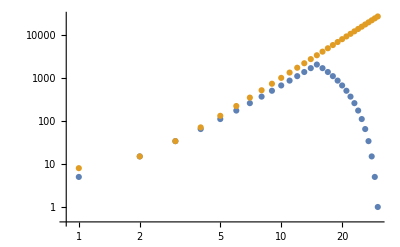

```mathematica
ListLogLogPlot@{counting,ns^3+7}
```

```mathematica
hafnian[n_]:=(2n-1)!!g[{n,{0,0,0}}];
```

## Plot coefficients of k

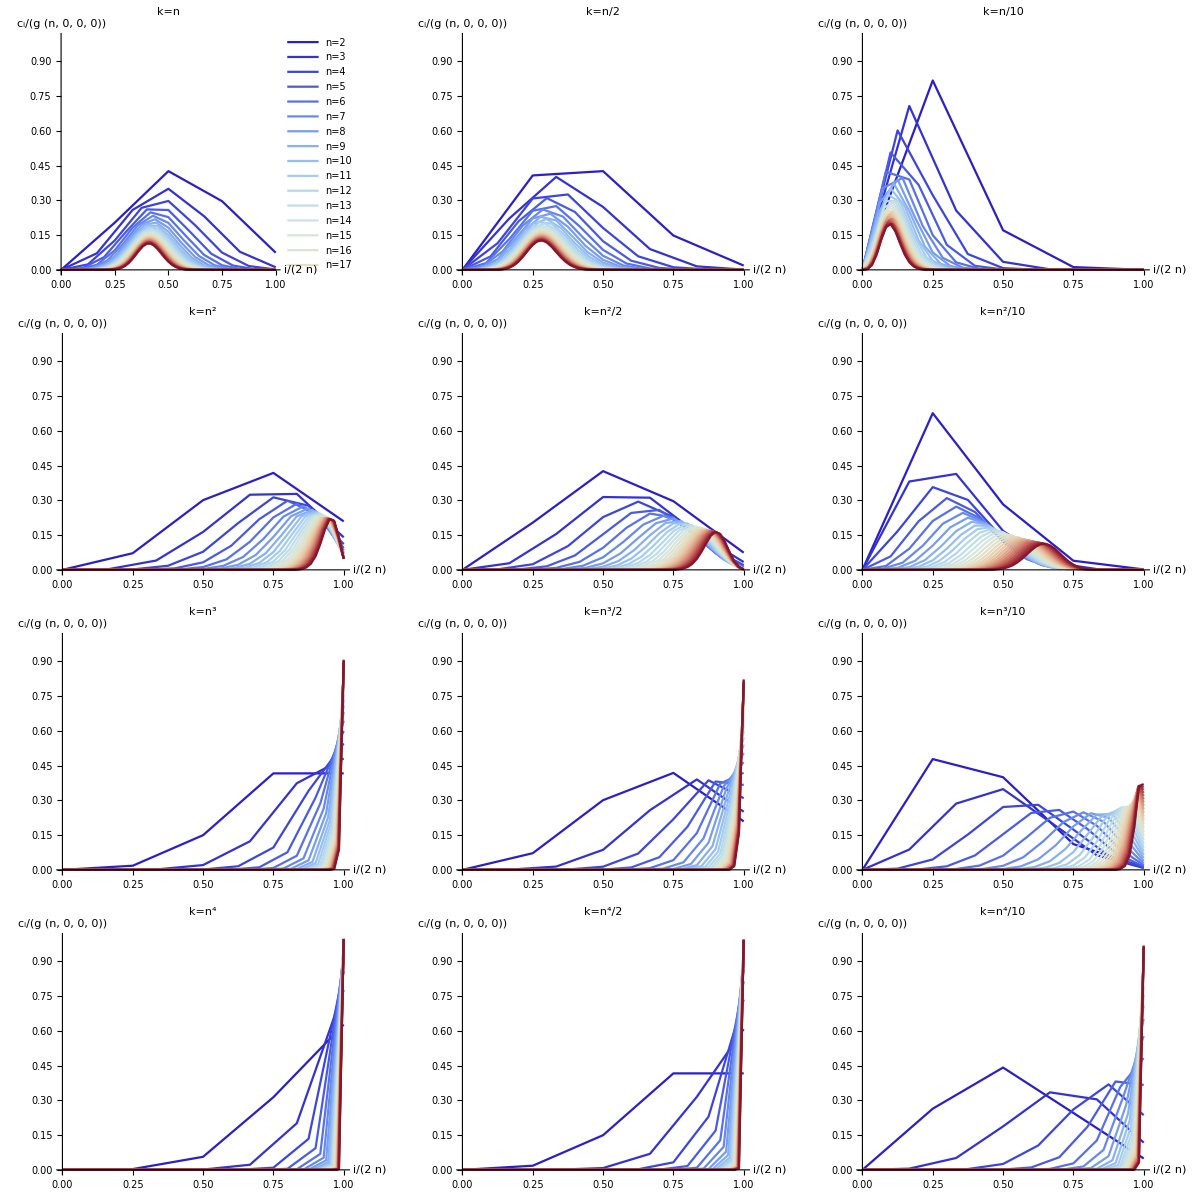

```mathematica
l[n_]:=CoefficientList[g[{n,{0,0,0}}],k];
t[n_,kk_]:=With[{ll=l@n,tot=g[{n,{0,0,0}}]/.k->kk@n},
Table[{(i-1)/(Length@ll-1),ll[[i]](kk@n)^(i-1)/tot},{i,Length@ll}]
];
linearmesh[a_,b_,n_Integer]:=Array[#&,n,{a,b}] (*Used for coloring with gradient*)
nslabels = Drop[Table["n="<>ToString[i],{i,ns}],1]; (* Used for legend *)
imageSize=350; imagePadding = {{40,30},{40,30}}; (* Grid parameters *)
plot[nns_,kk_,title_]:=ListPlot[Table[t[n,kk],{n,nns}],Joined->True,PlotRange->{0,1}, AxesLabel->{"i/(2  n)","c_i/(g (n, 0, 0, 0))"},ImageSize->imageSize,ImagePadding->imagePadding,PlotLabel->"k="<>title, PlotStyle -> "ThermometerColors"];
p1=plot[Drop[ns,1],#&,"n"] (* k = n *);p2=plot[Drop[ns,1],#/2&,"n/2"] (* k = n/2 *);p3=plot[Drop[ns,1],#/10&,"n/10"] (* k = n/10 *);
p4=plot[Drop[ns,1],#^2&,"n^2"] (* k = n^2 *);p5=plot[Drop[ns,1],#^2/2&,"n^2/2"] (* k = n^2/2 *);p6=plot[Drop[ns,1],#^2/10&,"n^2/10"] (* k = n^2/10 *);
p7=plot[Drop[ns,1],#^3&,"n^3"] (* k = n^3 *);p8=plot[Drop[ns,1],#^3/2&,"n^3/2"] (* k = n^3/2 *);p9=plot[Drop[ns,1],#^3/10&,"n^3/10"] (* k = n^3/10 *);
p10=plot[Drop[ns,1],#^4&,"n^4"] (* k = n^4 *);p11=plot[Drop[ns,1],#^4/2&,"n^4/2"] (* k = n^4/2 *);p12=plot[Drop[ns,1],#^4/10&,"n^4/10"] (* k = n^4/10 *);

distributionPlt = Legended[Grid[{{p1,p2,p3},{p4,p5,p6},{p7,p8,p9},{p10,p11,p12}},Spacings->{5,0}],LineLegend[(ColorData["ThermometerColors"])/@linearmesh[0,1,Length[nslabels]],nslabels]]
```

```mathematica
(*Export["distribution_plot.pdf",distributionPlt]*)
```

## Scaling and Structure of g(n,0,0,0)

#### Scaling of g(n,0,0,0)

```mathematica
lowerBound[k_]:= 2n Log[k] + 2 n Log[n] + (Log[4]-2)n + 1/2 Log[n] + 1/2 Log[4 π] + 1/(24 n + 1); (* Lower bound from Stirling's approximation *)
upperBound[k_]:= 2n Log[k]+ 4 n Log[n] + (3 Log[4] -4)n + (1-12n)/(6n(12n+1))+Log[4]; (* Upper bound from Stirling's approximation *)
lowerBoundAdjusted[k_] :=lowerBound [k]+ 1.94 n -2.68; (* Adjusted by the best fit for the difference between the leading and max terms *)
(* Note that this doesn't quite work as an approximation because it only brings the leading term to the largest term, whereas we would need to account for all of the terms, obviously. It still should give a lower bound, though, as we should essentially be replacing the lower bound based on the leading term with the lower bound based on the maxium term. *)
```

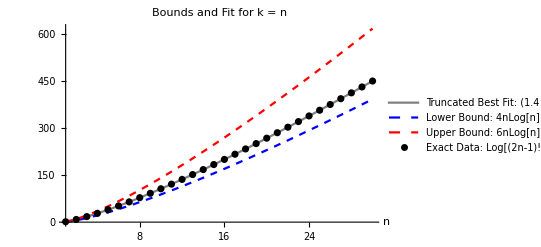

```mathematica
(* Make plot for k = n*)
data =  Table[{n,(Log[(2n-1)!!g[{n,{0,0,0}}]]/.{k->n})},{n,ns}];(* Create list of data points (n, E[|haf|^4]) *)
g000Factorial=Fit[ data,{1,n,Log[n],n*Log[n]},n]; (* Best fit using {1, n, Log[n], n Log[n]} as possible terms *)
g000FactorialTruncated=Fit[ data[[10;;Last[ns]]],{1,n,Log[n],n*Log[n]},n];(* Best fit using {1, n, Log[n], n Log[n]}; fit only to later data points *)
boundPlt = Legended[Show[
Plot[
{g000FactorialTruncated,lowerBound[n],upperBound[n]},{n,1,30},
PlotLabel->"Bounds and Fit for k = n",
AxesLabel->{"n",""},
PlotStyle->{{Gray,Thick},{Blue, Dashed, Thick},{Red,Dashed,Thick}}],
ListPlot[data,PlotStyle->Black]
],
{LineLegend[{Directive[Gray,Thick],Directive[Blue,Dashed,Thick],Directive[Red,Dashed,Thick]},
{"Truncated Best Fit:" g000FactorialTruncated /. a_?NumberQ:>Round[a,.01],
"Lower Bound:  4nLog[n] + (Log[4]-2)n + 1/2Log[n] + 1/2Log[4π] + 1/(24 n + 1)", 
"Upper Bound:  6nLog[n] + (3 Log[4] -4)n + (1-12n)/(6n(12n+1)) + Log[4]"}],
PointLegend[{Directive[Black,Circle]},{"         Exact Data: Log[(2n-1)!! × g(n,0,0,0)]"}]}
]
```

```mathematica
(*Export["bound_fit.pdf",boundPlt]*)
```

```mathematica
(* Make plot for k = n^2*)
```

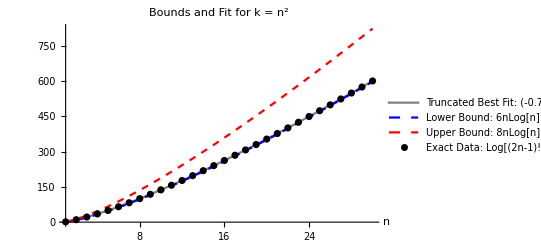

```mathematica
data =  Table[{n,(Log[(2n-1)!!g[{n,{0,0,0}}]]/.{k->n^2})},{n,ns}];(* Create list of data points (n, E[|haf|^4]) *)
g000FactorialTruncated=Fit[data[[10;;Last[ns]]],{1,n,Log[n],n*Log[n]},n];(* Best fit using {1, n, Log[n], n Log[n]}; fit only to later data points *)
boundPlt2 = Legended[Show[
Plot[
{g000FactorialTruncated,lowerBound[n^2],upperBound[n^2]},{n,1,30},
PlotLabel->"Bounds and Fit for k = n^2",
AxesLabel->{"n",""},
PlotStyle->{{Gray,Thick},{Blue, Dashed, Thick},{Red,Dashed,Thick}}],
ListPlot[data,PlotStyle->Black]
],
{LineLegend[{Directive[Gray,Thick],Directive[Blue,Dashed,Thick],Directive[Red,Dashed,Thick]},
{"Truncated Best Fit:" g000FactorialTruncated /. a_?NumberQ:>Round[a,.01],
"Lower Bound:  6nLog[n] + (Log[4]-2)n + 1/2Log[n] + 1/2Log[4π] + 1/(24 n + 1)", 
"Upper Bound:  8nLog[n] + (3 Log[4] -4)n + (1-12n)/(6n(12n+1)) + Log[4]"}],
PointLegend[{Directive[Black,Circle]},{"         Exact Data: Log[(2n-1)!! × g(n,0,0,0)]"}]}
]
```

#### Scaling of dominant term in g(n,0,0,0)

```mathematica
maxData = Map[Max, Table[((g[{n,{0,0,0}}][[i]])/g[{n,{0,0,0}}])/.{k-> n},{n,1,30},{i,1,2n}],{1}]//N ; (* Find max proportion for a single term for all n, k = n *)
leadingData = Table[((g[{n,{0,0,0}}][[2n]])/g[{n,{0,0,0}}])/.{k-> n},{n,1,30}]//N; (* Find proportion of total given by k^(2n) term *)
```

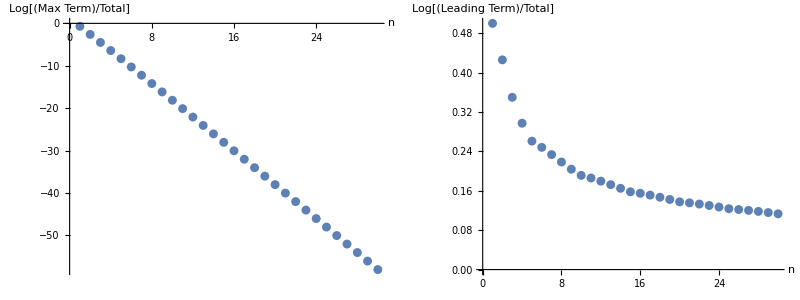

```mathematica
leadingPlot = ListPlot[Transpose[{ns,Log[leadingData]}],ImageSize->500,AxesLabel->{"n","Log[(Max Term)/Total]"}];
maxPlot = ListPlot[Transpose[{ns,maxData}],ImageSize->500,AxesLabel->{"n","Log[(Leading Term)/Total]"}];
Grid[{{leadingPlot, maxPlot}}, Spacings->{10}]
```

```mathematica
maxOverLeading =  Fit[ Transpose[{ns,Log[maxData/leadingData]}],{1,n,Log[n],n*Log[n]},n];
maxOverLeadingLinear =  Fit[ Transpose[{ns,Log[maxData/leadingData]}],{1,n},n]; (* Linear fit *)
```

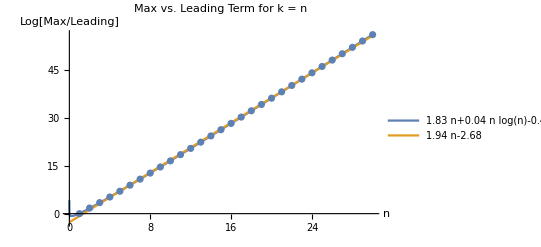

```mathematica
maxVsLeadingPlot = Show[
Plot[{maxOverLeading,maxOverLeadingLinear},{n,0,30},
PlotLabel->"Max vs. Leading Term for k = n",
AxesLabel->{"n","Log[Max/Leading]"},
PlotLegends->{maxOverLeading /. a_?NumberQ:>Round[a,.01],maxOverLeadingLinear /. a_?NumberQ:>Round[a,.01]}
],
ListPlot[Transpose[{Table[i,{i,1,30}],Log[maxData/leadingData]}]]
]
```

```mathematica
(*Export["max_vs_leading.pdf",maxVsLeadingPlot]*)
```

#### Gaussian Fit

```mathematica
termData[n_]:=  Table[((g[{n,{0,0,0}}][[i]])/g[{n,{0,0,0}}])/.{k-> n},{i,1,2*n}]; (* Normalize each term by the total g(n,0,0,0) *)
```

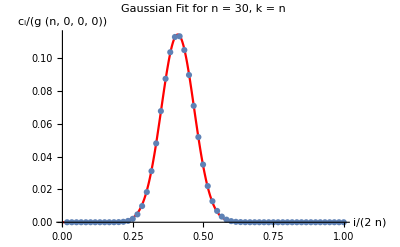

```mathematica
gaussianData=Transpose[{Table[i/(2*30),{i,1,2*30}],termData[30]}]; (* Create data *)
gaussianModel[x_]=A Evaluate[PDF[NormalDistribution[μ,σ],x]]; (* Gaussian model *)
gaussianFit=FindFit[gaussianData,gaussianModel[x],{A,μ,σ},x]; (* Fit to Gaussian *)
gaussianPlot=Show[
Plot[gaussianModel[x]/.gaussianFit,{x,0,1},PlotStyle->Red,PlotLabel->"Gaussian Fit for n = 30, k = n",
AxesLabel->{"i/(2  n)","c_i/(g (n, 0, 0, 0))",PlotRange->{0,1}},
PlotLegends->"(A SuperscriptBox[ⅇ, FractionBox[-SuperscriptBox[(FractionBox[i, 2  n] - μ), 2], 2 SuperscriptBox[σ, 2]]])/(√(2  π)), {A,μ,σ} = " <> ToString[Round[Values[gaussianFit],.001]]],
ListPlot[gaussianData,PlotRange->{0,1}]
]
```

```mathematica
(Values[gaussianFit][[1]])/(√(2π)Values[gaussianFit][[3]])(* Max Amplitude *)
```

0.114244

```mathematica
generalizedGaussianData[γ_,a_,n_]:=   Table[{i/(2n),(((g[{n,{0,0,0}}][[i]])/g[{n,{0,0,0}}])/.{k-> γ n^a})},{i,1,2*n}];
```

```mathematica
Manipulate[ListPlot[generalizedGaussianData[γ,a,Last[ns]],PlotRange->All],{γ,0.1,5},{a,0,3}]
```

```mathematica
(*Export["gaussian_plot.pdf",gaussianPlot]*)
```

```mathematica
(* Manipulate to see how distribution changes as a function of γ for k = γ n *)
Manipulate[
termData[n_]:=  Table[((g[{n,{0,0,0}}][[i]])/g[{n,{0,0,0}}])/.{k-> n^γ},{i,1,2*n}]; 
gaussianData=Transpose[{Table[i/(2*30),{i,1,2*30}],termData[30]}];
gaussianModel[x_]=A Evaluate[PDF[NormalDistribution[μ,σ],x]];
gaussianFit=FindFit[gaussianData,gaussianModel[x],{A,μ,σ},x];
gaussianPlot=Show[
Plot[gaussianModel[x]/.gaussianFit,{x,0,1},PlotStyle->Red,PlotLabel->"Gaussian Fit for n = 30, k = " <> ToString[Round[γ,0.01]] <> "n",
AxesLabel->{"i/(2  n)","c_i/(g (n, 0, 0, 0))"},
PlotLegends->"A ⅇ^((-SuperscriptBox[(FractionBox[i, 2  n] - μ), 2])/(2 SuperscriptBox[σ, 2])), {A,μ,σ} = " <> ToString[Round[Values[gaussianFit],.001]],
PlotRange->All],
ListPlot[gaussianData]
],
{γ,0,3}

]
```

#### Constants:

Investigate the linear and largest coefficients to figure out where all of the graphs are. There should be [(2n-1)!!]^3 4^n in total, meaning we need to find large constant coefficients with log somewhere.

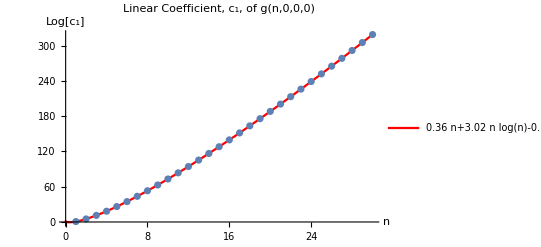

```mathematica
linearData =Table[(g[{n,{0,0,0}}][[1]])/.{k-> 1},{n,1,30}]//N ; (* Find linear constant *)
linearFit =  Fit[ Transpose[{ns,Log[linearData]}],{1,n,Log[n],n*Log[n]},n];
linearPlot = Show[
Plot[{linearFit},{n,0,30},
PlotLabel->"Linear Coefficient, c_1, of g(n,0,0,0)",
AxesLabel->{"n","Log[c_1]"},
PlotLegends->{linearFit /. a_?NumberQ:>Round[a,.01]},
PlotStyle->Red
],
ListPlot[Transpose[{ns,Log[linearData]}],ImageSize->500]
]
```

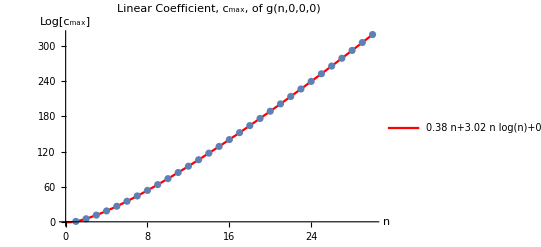

```mathematica
maxConstantData =Map[Max,Table[(g[{n,{0,0,0}}][[i]])/.{k-> 1},{n,1,30},{i,1,2n}],{1}] ; (* Find max constant *)
maxFit =  Fit[ Transpose[{ns,Log[maxConstantData]}],{1,n,Log[n],n*Log[n]},n];
maxConstantPlot = Show[
Plot[{maxFit},{n,0,30},
PlotLabel->"Linear Coefficient, c_max, of g(n,0,0,0)",
AxesLabel->{"n","Log[c_max]"},
PlotLegends->{maxFit /. a_?NumberQ:>Round[a,.01]},
PlotStyle->Red
],
ListPlot[Transpose[{ns,Log[maxConstantData]}],ImageSize->500]
]
```

```mathematica
(*Plot all coefficients for all n to see the distribution*)
constantsPlt1 = ListLinePlot[Table[{i/(2*n),Log[g[{n,{0,0,0}}][[i]]]},{n,2,30},{i,1,2n}]/.{k->1},PlotRange->{0,400},AxesLabel->{"i/(2n)","Log[c_i]"},PlotStyle->"ThermometerColors",ImageSize->400];
constantsPlt2 = ListLinePlot[Table[{i/(2*n),Log[g[{n,{0,0,0}}][[i]]]/Log[(2n)!!]},{n,2,30},{i,1,2n}]/.{k->1},PlotRange->{0,10},AxesLabel->{"i/(2n)","Log[SubscriptBox[c, i]]/Log[(2  n)!!]"},PlotStyle->"ThermometerColors",ImageSize->400];
```

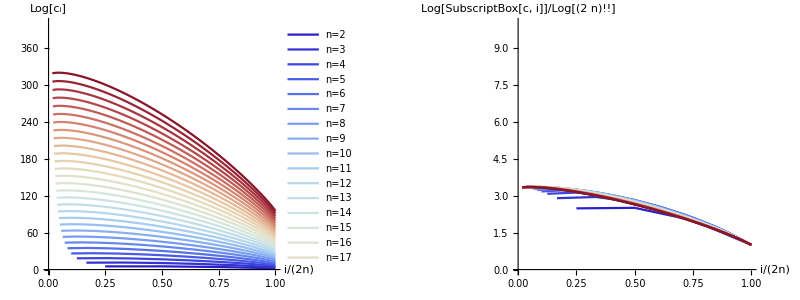

```mathematica
constantsPlt = Legended[Grid[{{constantsPlt1,constantsPlt2}},Spacings->{5,0}],LineLegend[(ColorData["ThermometerColors"])/@linearmesh[0,1,Length[nslabels]],nslabels]]
```

```mathematica
(*Export["constants.pdf",constantsPlt]*)
```

```mathematica
(*Truncated version of the above to show how well it collapses*)
```

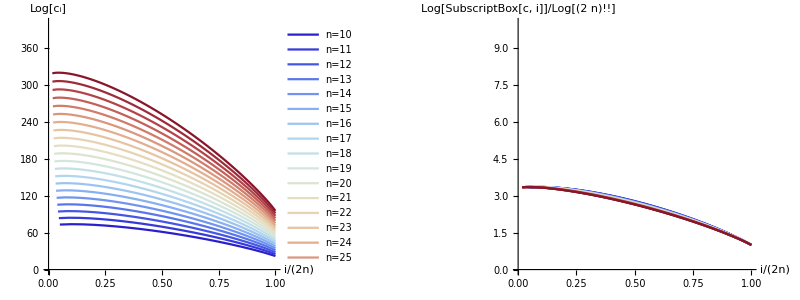

```mathematica
constantsPlt1Truncated = ListLinePlot[Table[{i/(2*n),Log[g[{n,{0,0,0}}][[i]]]},{n,10,30},{i,1,2n}]/.{k->1},PlotRange->{0,400},AxesLabel->{"i/(2n)","Log[c_i]"},PlotStyle->"ThermometerColors",ImageSize->400];
constantsPlt2Truncated = ListLinePlot[Table[{i/(2*n),Log[g[{n,{0,0,0}}][[i]]]/Log[(2n)!!]},{n,10,30},{i,1,2n}]/.{k->1},PlotRange->{0,10},AxesLabel->{"i/(2n)","Log[SubscriptBox[c, i]]/Log[(2  n)!!]"},PlotStyle->"ThermometerColors",ImageSize->400];
constantsPltTruncated = Legended[Grid[{{constantsPlt1Truncated,constantsPlt2Truncated}},Spacings->{5,0}],LineLegend[(ColorData["ThermometerColors"])/@linearmesh[0,1,Length[nslabels[[9;;Length[nslabels]]]]],nslabels[[9;;Length[nslabels]]]]]
```

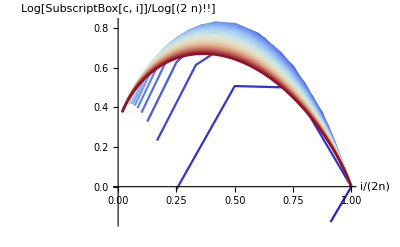

```mathematica
constantsPlt3 = ListLinePlot[Table[{i/(2n),Log[g[{n,{0,0,0}}][[i]]]/Log[(2n)!!]+2 i/(2n)-3},{n,1,30},{i,1,2n}]/.{k->1},AxesLabel->{"i/(2n)","Log[SubscriptBox[c, i]]/Log[(2  n)!!]"},PlotStyle->"ThermometerColors",ImageSize->400]
```

```mathematica
Fit[Table[{i/(2*30),Log[g[{30,{0,0,0}}][[i]]]/Log[(2*30)!!]-i/(2*30)},{i,1,2*30}]/.{k->1},{1,i,i^2},{i}]
```

3.39884-1.61276 i-1.76287 i^2

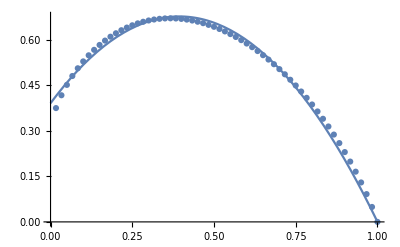

```mathematica
Show[{Plot[Evaluate[(a + b i + c i^2/.FindFit[Table[{i/(2*30),Log[g[{30,{0,0,0}}][[i]]]/Log[(2*30)!!]+2 i/(2*30)-3},{i,1,2*30}]/.{k->1},{a + b i + c i^2,a + b + c == 0},{a,b,c},i])],{i,0,1}],
ListPlot[Table[{i/(2*30),Log[g[{30,{0,0,0}}][[i]]]/Log[(2*30)!!]+2 i/(2*30)-3},{i,1,2*30}]/.{k->1}]}
]
```

```mathematica
maxConstantProportionData =Map[Max,Table[(g[{n,{0,0,0}}][[i]])/g[{n,{0,0,0}}]/.{k-> 1},{n,1,30},{i,1,2n}],{1}]//N; (* Find proportion of graphs max term covers for all n *)
```

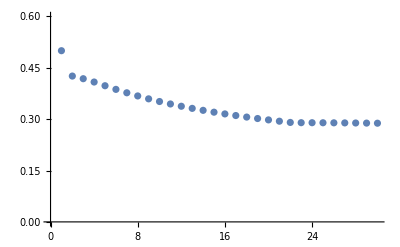

```mathematica
ListPlot[Transpose[{ns,maxConstantProportionData}],PlotRange->{0,0.6}]
```

#### Normalizing (NOT COMPLETE)

```mathematica
secondMoment[n_,k_]:= (2n-1)!!*((k+2(n-1))!!)/((k-2)!!);
lowerBoundNormalized[n_,k_]:= √(π n/8) * ⅇ^(2n)*1/(1+(2n)/(k-1))^(k+2n-1);
upperBoundNormalized[n_,k_]:= √2* 4^(2n+1)n^(2n)*1/(1+(2n-1)/k)^(k+2n-1);
lowerBoundNormalizedLogSimplified[n_,k_]:= 1/2 Log[n]+1/2 Log[π/8] + 2n(-1/(k-1))-(2n(2n-1))/(k-1);
datan = Table[{n,Log[(((2n-1)!!g[{n,{0,0,0}}])/.{k->n})/(secondMoment[n,n])^2]},{n,1,30}];
datan2 = Table[{n,Log[(((2n-1)!!g[{n,{0,0,0}}])/.{k->n^2})/((secondMoment[n,n^2])^2)]},{n,1,30}];
datan3 = Table[{n,Log[(((2n-1)!!g[{n,{0,0,0}}])/.{k->n^3})/((secondMoment[n,n^3])^2)]},{n,1,30}];
datan4 = Table[{n,Log[(((2n-1)!!g[{n,{0,0,0}}])/.{k->n^4})/((secondMoment[n,n^4])^2)]},{n,1,30}];
lowerBoundNormalizedn = Table[{n,Log[lowerBoundNormalized[n,n]]},{n,2,30}];
upperBoundNormalizedn = Table[{n,Log[upperBoundNormalized[n,n]]},{n,2,30}];
(*lowerBoundNormalizedn2 = Table[{n,Log[lowerBoundNormalized[n,n^2]]},{n,2,30}];
lowerBoundNormalizedn3 = Table[{n,Log[lowerBoundNormalized[n,n^3]]},{n,2,30}];
lowerBoundNormalizedn4 = Table[{n,Log[lowerBoundNormalized[n,n^4]]},{n,2,30}];*)
```

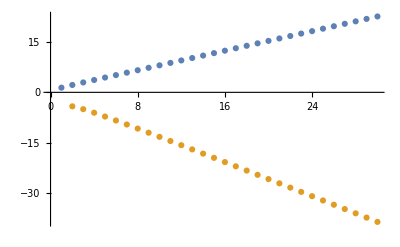

```mathematica
ListPlot[{datan,lowerBoundNormalizedn}]
```

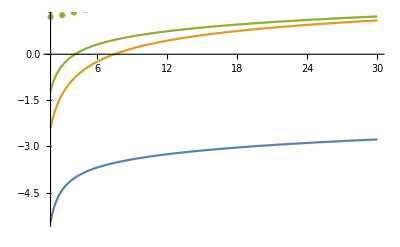

```mathematica
Show[{Plot[{lowerBoundNormalizedLogSimplified[n,n^2],lowerBoundNormalizedLogSimplified[n,n^3],lowerBoundNormalizedLogSimplified[n,n^4]},{n,2,30}],ListPlot[{datan2,datan3,datan4}]}]
```

```mathematica
(* Plot normalized best fits for k = n and k = n^2*)
dataNormalizedn = Table[{n,Log[((2n-1)!!g[{n,{0,0,0}}]/.{k->n})/(secondMoment[n,n])^2]},{n,ns}];
dataNormalizedn2 = Table[{n,Log[((2n-1)!!g[{n,{0,0,0}}]/.{k->n^2})/((secondMoment[n,n^2])^2)]},{n,ns}];
fitTruncatedNormalizedn=Fit[ dataNormalizedn[[10;;Last[ns]]],{1,n},n];
fitTruncatedNormalizedn2=Fit[ dataNormalizedn2[[10;;Last[ns]]],{1,Log[n]},n];
plt =Legended[ Show[{
Plot[
{fitTruncatedNormalizedn,fitTruncatedNormalizedn2},{n,0.5,30},
PlotLabel->MaTeX["\\text{Normalized Best Fits}"],
AxesLabel->{MaTeX["n"],MaTeX["    \\log \\left[ \\
\\frac{\\mathbb{E}[|\\mathrm{Haf}|^{4}]}{\\left(\\mathbb{E}[|\\mathrm{Haf}|^{2}]\\right)^{2}}\\right]"]}],
ListPlot[{dataNormalizedn,dataNormalizedn2},PlotStyle->{{Black},{Black}},PlotMarkers->{"x","*"}]
}],
{LineLegend[{Directive[Blue,Thick],Directive[Orange,Thick]},
{MaTeX["k=n \\text{ Best Fit: } 0.73 n + 0.76"],
MaTeX["k=n^{2} \\text{ Best Fit: } 0.6\\log n + 1.42"]}
],
PointLegend[{Black, Black},{MaTeX["k=n \\text{ Exact Data}"],MaTeX["k=n^{2} \\text{ Exact Data}"]}, LegendMarkers-> {"x","*"}
]}
]
```

-Graphics-

```mathematica
(* Manipulate showing how fit goes from exponential to polynomial *)
Manipulate[
ListPlot[{dataNormalizedn,dataNormalizedn2, Table[{n,Log[((2n-1)!!g[{n,{0,0,0}}]/.{k->n^a})/((secondMoment[n,n^a])^2)]},{n,ns}] },
PlotRange->{0,40},
PlotStyle->{{Black},{Black},{Black}},PlotMarkers->{"x","*", "o"},PlotLegends->{"","",Fit[ Table[{n,Log[((2n-1)!!g[{n,{0,0,0}}]/.{k->n^a})/((secondMoment[n,n^a])^2)]},{n,10,Last[ns]}],{1,n,Log[n]},{n}]}],
{a,0,3}]
```

```mathematica
(*(* Create an animation interpolating a ∈ [1,2] for k = n^a *)
normalizationAnimation = Animate[
ListPlot[{dataNormalizedn,dataNormalizedn2, Table[{n,Log[((2n-1)!!g[{n,{0,0,0}}]/.{k->n^a})/((secondMoment[n,n^a])^2)]},{n,ns}] },PlotStyle->{{Black},{Black},{Black}},PlotMarkers->{"x","*", "o"}],
{a,1,2}]*)
```

```mathematica
(*Export["normalization_animation.gif",normalizationAnimation]*)
```

#### ATTEMPT at extracting constants

```mathematica
(* Try to extract constants for constant, linear, log terms*)
```

```mathematica
γArray = Table[γ, {γ,.1,5,.1}];
aArray = Table[a, {a,0,3,.1}];
```

```mathematica
fitArray = Table[{γ,a,Fit[ Table[{n,Log[((2n-1)!!g[{n,{0,0,0}}]/.{k->γ n^a})/((secondMoment[n,n^a])^2)]},{n,10,Last[ns]}],{1,Log[n],n},{n}]},{γ,γArray},{a,aArray}];
```

General::munfl: 8.71613×10^270 7.198149059×10^-330 is too small to represent as a normalized machine number; precision may be lost.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::munfl: 3.54428×10^279 1.024202575×10^-338 is too small to represent as a normalized machine number; precision may be lost.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::munfl: 1.88277×10^275 1.331455155×10^-332 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Fit::fitm: Unable to solve for the fit parameters; the design matrix is nonrectangular, non-numerical, or could not be inverted.

General::stop: Further output of Fit::fitm will be suppressed during this calculation.

```mathematica
fitArray[[12]][[17]][[3]]
```

0.406162+0.408809 n+1.04679 Log[n]

```mathematica
linearCoefficientList = Table[{γArray[[i]],aArray[[j]],Coefficient[fitArray[[i]][[j]][[3]],n,1]},{i,1,Length[γArray]},{j,1,Length[aArray]}];
```

```mathematica
logCoefficientList = Table[{γArray[[i]],aArray[[j]],Coefficient[fitArray[[i]][[j]][[3]],Log[n],1]},{i,1,Length[γArray]},{j,1,Length[aArray]}];
constantCoefficientList = fitArray-n * linearCoefficientList - Log[n] * logCoefficientList;
```

```mathematica
linearCoefficientList[[12]][[17]][[3]]
logCoefficientList[[12]][[17]][[3]]
constantCoefficientList[[12]][[17]][[3]]
```

0.408809

1.04679

0.406162

```mathematica
ListPlot3D[Flatten[logCoefficientList,1]]
```

-Graphics3D-

```mathematica
logCoefficientList[[All,9]][[All,3]]
```

{-2.19052,-2.00316,-1.82104,-1.65139,-1.49422,-1.34827,-1.21221,-1.08485,-0.965182,-0.852366,-0.745695,-0.644569,-0.548478,-0.456981,-0.369697,-0.286293,-0.206474,-0.129981,-0.0565823,0.0139296,0.0817415,0.147022,0.209925,0.27059,0.329145,0.385707,0.440384,0.493276,0.544476,0.594068,0.642133,0.688745,0.733974,0.777884,0.820536,0.861988,0.902292,0.941501,0.979661,1.01682,1.05301,1.08829,1.12268,1.15622,1.18896,1.22091,1.25212,1.28261,1.3124,1.34153}

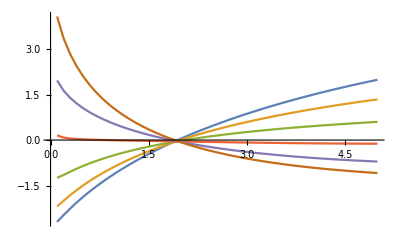

```mathematica
ListLinePlot[
{
Transpose[{γArray,logCoefficientList[[All,8]][[All,3]]}],
Transpose[{γArray,logCoefficientList[[All,9]][[All,3]]}],
Transpose[{γArray,logCoefficientList[[All,10]][[All,3]]}],
Transpose[{γArray,logCoefficientList[[All,11]][[All,3]]}],
Transpose[{γArray,logCoefficientList[[All,12]][[All,3]]}],
Transpose[{γArray,logCoefficientList[[All,13]][[All,3]]}]
}
]
```

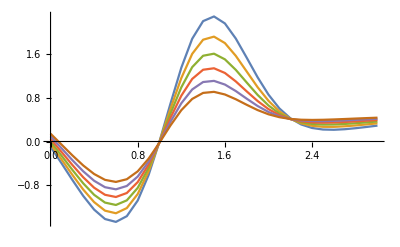

```mathematica
ListLinePlot[
{
Transpose[{aArray,logCoefficientList[[8,All]][[All,3]]}],
Transpose[{aArray,logCoefficientList[[9,All]][[All,3]]}],
Transpose[{aArray,logCoefficientList[[10,All]][[All,3]]}],
Transpose[{aArray,logCoefficientList[[11,All]][[All,3]]}],
Transpose[{aArray,logCoefficientList[[12,All]][[All,3]]}],
Transpose[{aArray,logCoefficientList[[13,All]][[All,3]]}]
}
]
```